# Corporate Sustainability Assessment with BERT

## Understanding enterprise report content using state of the art Natural Language processing techniques

Team Roche  | Mathieu Bélanger,Sybille Roemer,Yanis Cuche

Abstract : In this project, we first trained a classifier that can detect whether a sentence is related to the SDGs (positive) or not (negative). Then, we collected the sustainable reports of many public companies, to measure the corresponding similarity to SDG-related contents.

Drastic increases of greenhouse gases after the industrial revolution

Big companies have a huge environmental and societal impact

In 2015, the United Nation created the concept of "Sustainable development goals" to encourage firms to take action against poverty and planet damage.

Divided into 17 SDGs with each different target (169)

The ESG score indicates the performance of companies regarding the above mentioned SDG. Here we can see the how the increase of CO2 emissions coincide with the second industrial revolution.

Here we can see the how the increase of CO2 emissions coincide with the second industrial revolution. [1]

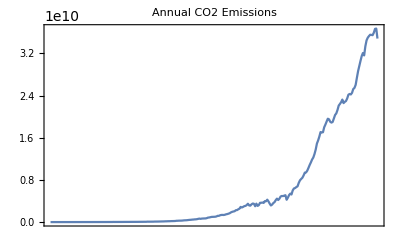

```mathematica
data=Import["https://raw.githubusercontent.com/0xMarmelade/mgt-492-data-science/master/annual-co2-emissions-per-country.csv", "Dataset", HeaderLines -> 1];
Yeardata=Normal @ data[All,"Year"];
emissionsdata=Normal@data[All, "Annual CO2 emissions"];
Asso=AssociationThread[Yeardata->emissionsdata];
DateListPlot[Asso,PlotLabel->"Annual CO2 Emissions", DateTicksFormat->{"Year"} ]
```

## 2. Methodology

Collection of :

Sustainability report of 115 companies

Text from Wikipedia and other Web sources containing  :

sentences related to the sustainable development goal

sentences unrelated to the sustainable development

Text is processed on a sentence basis using DistilBERT

BERT is state of the art in language representation techniques

DistillBERT taken from the Wolfram Neural Net repository is a pretrained model using Wikipedia Article data and the Book Corpus dataset

However Enterprise annual & sustainability reports can be prohibitively large (1200+ sentences) for deep learning techniques

Strategies are employed to reduce the input data size

One efficient fix is to randomly sample sentences from the reports (~100)

Training of a classifier to recognize sentences related to SDG

Use of this classifier to extract the number of SDG related sentences

```mathematica
Import["https://github.com/0xMarmelade/mgt-492-data-science/raw/master/Corporate%20sustainability%20(1).jpeg"]
```

-Graphics-

## 3. Training a classifier to recognize SDG-related sentences

### 3.1 Import of positive & negative sentences for training

To train our model, we took on Wikipedia approximately 1000 sentences related to the SDGs (positive), according to a specific list of key words, and 1000 sentences that were not related (negative).

```mathematica
positiveTrain = 
  Import["https://raw.githubusercontent.com/0xMarmelade/mgt-492-data-science/master/sdg_sentences.txt"];
negativeTrain = 
  Import["https://raw.githubusercontent.com/0xMarmelade/mgt-492-data-science/master/non_sdg_sentences.txt"];
```

Here we use the function TextSentences, to segment the text into full sentences.

```mathematica
{positiveTrain, negativeTrain} = 
  TextSentences /@ {positiveTrain, negativeTrain};
```

```mathematica
positiveTrain[[1 ;; 2]]
```

{Development Goals (SDGs) or Global Goals are a collection of 17 interlinked global goals designed to be a "blueprint to achieve a better and more sustainable future for all".,The SDGs were set up in 2015 by the United Nations General Assembly (UN-GA) and are intended to be achieved by the year 2030.}

### 3.2 Initialization of the BERT (DistillBERT) embedding model

Bert is a tool that can understand and analyze language. It stands for "Bidirectional Encoder Representations from Transformers". We use this powerful tool to retrieve SDGs-related and non-SDGs-related sentences, as it is able to get their context. The bert model outputs data in the form of matrices that represent embedding vectors:

```mathematica
Import["https://jalammar.github.io/images/bert-transfer-learning.png"]
```

-Graphics-

```mathematica
bertEmbedder = NetModel["DistilBERT Trained on BookCorpus and English Wikipedia Data"]
```

NetChain[…]

BERTs output dense matrices representing the sentence's content & structure. These matrices can then be compared and classified using relevant techniques:

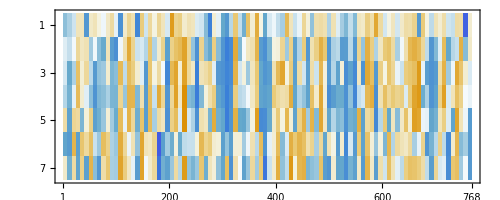

```mathematica
bertEmbedder["This is an example."];
MatrixPlot @%
```

### 3.3 Creating subword embeddings for SDG & non-SDG sentences

Now, we want to create subword embeddings, so we respectively associate the SDGs-related sentences to the label "positive", and the others to "negative", using the AssociationThread function.

```mathematica
positiveEmbeddings = 
  AssociationThread[
   bert[#] & /@ positiveTrain[[interval]] -> "positive"];
negativeEmbeddings = 
  AssociationThread[
   bert[#] & /@ negativeTrain[[interval]] -> "negative"];
```

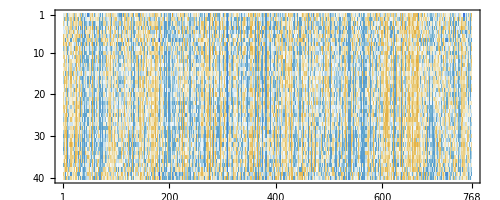

```mathematica
MatrixPlot @ First @ Keys @ positiveEmbeddings
```

```mathematica
Join[positiveEmbeddings, negativeEmbeddings];
```

```mathematica
dataTotal = 
  Dataset @ 
   MapThread[<|"Input" -> #1, "Output" -> #2|> &, {Keys @ %, 
     Values @ %}];
```

### 3.4 Defining the neural net classifier

Now that we have associated the sentences of our dataset with the positive and negative labels, we create a Neural net Classifier, that allows us to determine whether a random sentence is related (or not) to sustainability.

As a good-enough working design, we used the classifier net specified in the Wolfram Neural Net Repository neat examples section. [2]

```mathematica
classifierSDGSentences = 
 NetChain[{DropoutLayer[], NetMapOperator[2], 
   AggregationLayer[Max, 1], SoftmaxLayer[]}, 
  "Output" -> NetDecoder[{"Class", {"negative", "positive"}}]]
```

NetChain[…]

Here, a classic split of 80% / 20% is used to test the trained model

```mathematica
{dataTrain, dataTest} = 
  TakeDrop[RandomSample[dataTotal], 
   Round[First @ Dimensions @ dataTotal*0.8, 1]];
```

```mathematica
Dimensions /@ {dataTrain, dataTest}
```

```mathematica
{{649,2},{162,2}}
```

### 3.4 Training time!

```mathematica
distilbertresults = NetTrain[classifierSDGSentences, dataTrain, All,
  ValidationSet -> dataTest,
  TargetDevice -> "CPU",
  MaxTrainingRounds -> 100]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2100  rounds:100  time:26s  examples/s:2677
data | ,,  training examples:649  validation examples:162  processed examples:67200  skipped examples:0
method | ,,  ADAMoptimizer  batch size32CPU
round | ,,  loss:8.37×10^-3  error:0.149%
validation | ,,  loss:1.61×10^-2  error:0%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

It looks lire our model learns quite well the embeddings that we feed him (almost null errorRate, decreasing loss), with almost no overfitting with respect to the testing data. However, our training data was limited, only using Wikipedia texts and only built on a limited number of different Wikipedia articles/subject. There is a high chance that on multiple occasions sentences from the same articles were sampled both in the training AND testing set, resulting in hierarchical data leakage. In a sense we overfit to specific subjects selected while building our dataset. To account for this "leak" we would need to collect data from more different articles & sources and do the train/test split while keeping in the same group sentences from the same article. Doing so there would be less chances of our model only learning to recognize specific subjects and not generalizing to other SDG related ones (overfitting).

```mathematica
distilbertresults["ValidationMeasurements"]
```

<|Loss→0.0161033,ErrorRate→0.|>

### 3.5 Does it work?

We can test our Classifier with example sentences, to see whether  they are positive or negative.

```mathematica
distilbertresults["TrainedNet"] @ 
 bert["This section is an excerpt from Sustainable Development Goal \
4."]
```

positive

```mathematica
distilbertresults["TrainedNet"] @ 
 bert["In recent decades, states modeled some of their assets and enterprises after business enterprises. "]
```

negative

#### Dynamic input box can also be used to assess the SDGness of an input

```mathematica
DynamicModule[{text=""},Column[{InputField[Dynamic[text],String, FieldHint->"Enter a sentence"],Dynamic[distilbertresults["TrainedNet"] @ 
 bert[ {text}]]}]]
```

## 4. Applying the classifier to Enterprise sustainability reports to measure corresponding similarity to SDG-related contents

With our classifier, we can now evaluate the sentences of Sustainability reports of many public companies, by comparing their similarity to SDGs-related contents. To do so, we looked online for the Sustainability reports of 115 public companies.

```mathematica
dataTotal = 
  Import["https://gist.githubusercontent.com/0xMarmelade/\
124281e1c94d9f175781e04c3b4a1d20/raw/\
361a68d2b0e3168251b31c1c101c2b2ef9566bb4/Srep.csv", "Dataset", 
   HeaderLines -> 1];
RandomSample[dataTotal, 2]
```

#### 4.1 Preprocessing

The same pre-processing is applied to the report's text (data reduction, sampling & BERT embedding) than during training.

```mathematica
extractedSentences = dataTotal[interval, {3 -> TextSentences}];
```

```mathematica
MappedBert[x_] := bert /@ RandomSample[x, 100]
sentencesEmbeddings = extractedSentences[interval, {"text" ->   MappedBert}];
```

#### 4.2 Computing the predictions

```mathematica
reportsResult = sentencesEmbeddings[interval, {"text" -> Map[distilbertresults["TrainedNet"], # &]}];
```

```mathematica
SDGRatio[x_] := Round[Count[x ,"positive"]/ Length[x], 0.01];
```

#### 4.3 Results

According to our model, the CSR reports from the dataset present a variable share of SDG related content.

```mathematica
reportsResult[interval, {"text" -> SDGRatio} ]
```

The relatively high rate count of SDG sentences in the reports (which are sustainability reports) is not surprising.  However we can see that there is a high variability in the reported SDG sentence ratio, which tells us that we probably did not train on enough positive-sdg different subjects and text type.

## 5. Submit the annual report of your favorite green company!

```mathematica
reportText=Import[InputString["Please enter the direct url of an Enterprise Annual report"],"Plaintext"];
reportSentences=TextSentences[reportText];
bert[RandomSample[RemoveShortSentences @ reportSentences, 150]];
reportResults = distilbertresults["TrainedNet"]/@%;
```

According to our model, this enterprise dedicated this share of their report to SDG related content:

```mathematica
PercentForm @ Round[Count[reportResults, "positive"]/ Length @ reportResults, 0.01]
```

62%

The above number (62%) was generated using Roche's general annual repport, hence the SDG sentence ratio should reasonably be lower than the ones of the sustainability reports in section 4. Even if this is only a single example, it shows us that we lacked negative labeled examples in our training set that could generalized to this company's writing, presentation style and subject selection .

## 5. Sources

[1] https://ourworldindata.org/co2-emissions

[2] https://resources.wolframcloud.com/NeuralNetRepository/resources/DistilBERT-Trained-on-BookCorpus-and-English-Wikipedia-Data/